## Data

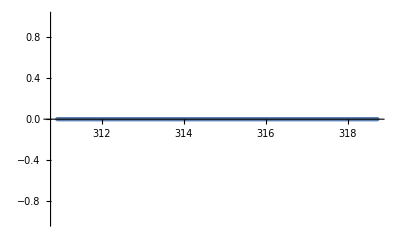

```mathematica
notePath = NotebookDirectory[];
fileName = "inputData\\noise\\397_CAP_NOISE.txt";
fullName = StringJoin[{notePath, "\\", fileName}];;
data = Import[fullName, "Data"][[2;;-2]];
dataPlot = ListPlot[data]
values = data[[All,2]];
```

## Fitting

0.343864

| Estimate | Standard Error | t-Statistic | P-Value
B0 | 0.343864 | 0.0104409 | 32.9345 | 1.73609×10^-55

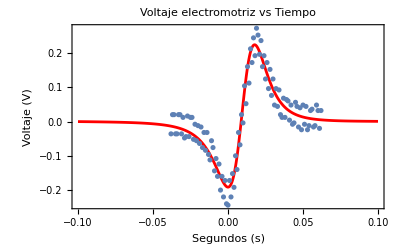

```mathematica
Clear[B0]
fitModel = NonlinearModelFit[data, AccelVoltageShifted[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.1}, PlotStyle->Red, PlotRange->All];

accelPlot = Plot[AccelVoltageShifted[t], {t,-0.06, 0.06}, PlotStyle->Green , PlotRange->All];

B0Fitted = B0/.fitModel["BestFitParameters"]
parameterTable = fitModel["ParameterTable"]

Show[fitPlot, dataPlot, accelPlot, PlotLabel->"Voltaje electromotriz vs Tiempo", Frame->True, FrameLabel->{"Segundos (s)", "Voltaje (V)"}]
```